# Golden Triangle

### Author

Eric W. Weisstein
February 16, 2025

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Triangles/GoldenTriangle.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/GoldenTriangle.html.

©2025 Wolfram Research, Inc. except for portions noted otherwise

### Deifnitions

```mathematica
ineq=-a/2≤x≤a/2&&0≤y≤(1-Abs[x/(a/2)]) a Sqrt[5+2Sqrt[5]]/2;
```

```mathematica
implreg=ImplicitRegion[ineq,{x,y}];
```

```mathematica
reg=Triangle[{{-a/2,0},{a/2,0},{0,Sqrt[5+2Sqrt[5]]/2 a}}];
```

```mathematica
assum=a>0;
```

## Figure

```mathematica
a=GoldenRatio;
b=1;
y=Sqrt[a^2-(b/2)^2];
```

```mathematica
Show[Graphics[{Line[{{-b/2,0},{b/2,0},{0,y},{-b/2,0}}],
Dashing[{.04}],Line[{{0,0},{0,y}}]
}],
AspectRatio->Automatic]
```

⁃Graphics⁃

## Figures

```mathematica
v1=Transpose[Through[{Cos,Sin}[2Pi Range[0,10,2]/5]]];
```

```mathematica
v2=Transpose[Through[{Cos,Sin}[2Pi Range[0,10]/10]]];
```

```mathematica
Show[GraphicsArray[Graphics[#,AspectRatio->Automatic]&/@
{
Line[v1],
{Line[v2],Line/@Transpose[Partition[v2,5]]}
}]]
```

⁃GraphicsArray⁃

## Plots

### Diagram

```mathematica
LaminaData["FilledGoldenTriangle","Diagram"]
```

-Graphics-

### DiscretizeRegion

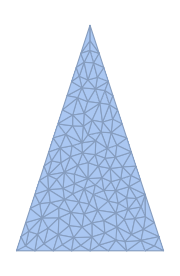

```mathematica
Block[{a=1},Show[DiscretizeRegion[reg],ImageSize->Small]]
```

### RegionPlot

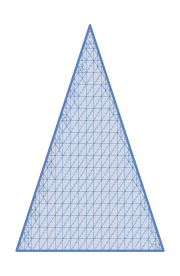

```mathematica
Block[{a=1},RegionPlot[ineq,{x,-a/2,a/2},{y,0,Sqrt[5+2Sqrt[5]]/2},AspectRatio->Automatic,ImageSize->Small,Frame->False]]
```

## Identities

### 1/2 csc(π/10)==ϕ

```mathematica
Csc[Pi/10]/2
```

1/2 (1+√5)

### 2 sin^-1(1/(2 ϕ))==π/5

```mathematica
FullSimplify[2ArcSin[1/(2GoldenRatio)]]
```

π/5

### 5^(1/4) ϕ^(3/2)==√(5+2 √5)

```mathematica
FullSimplify[ 5^(1/4)GoldenRatio^(3/2)- √(5+2 √5)]
```

0

## Properties

### Area

#### Area

```mathematica
Assuming[assum,Simplify@Area[reg]]
```

1/4 √(5+2 √5) a^2

#### Integrate

```mathematica
FullSimplify[1/2 b h]
```

1/4 √(5+2 √5) b^2

```mathematica
Assuming[a>0,MyArea[ineq,{x,y}]]//FullSimplify
```

1/4 √(5+2 √5) a^2

```mathematica
5^(1/4)/4 GoldenRatio^(3/2)-1/4 √(5+2 √5)//FullSimplify
```

0

#### RegionMeasure

```mathematica
Assuming[assum,Simplify@RegionMeasure[reg]]
```

1/4 √(5+2 √5) a^2

### AreaInertiaTensor

```mathematica
FullSimplify[{{(a h^3)/12,0},{0,(a^3 h)/48}}/.a->b,b>0]
```

{{1/96 (5+2 √5)^(3/2) b^4,0},{0,1/96 √(5+2 √5) b^4}}

```mathematica
√Expand[(5+2 √5)^3]//FullSimplify
```

√(5 (85+38 √5))

### Centroid

#### Integrate

```mathematica
{0,(a h^2)/6}/.a->b
```

{0,1/24 (5+2 √5) b^3}

```mathematica
Assuming[a>0,Centroid[ineq,{x,y}]]//FullSimplify
```

{0,1/6 √(5+2 √5) a}

```mathematica
5^(1/4)/6 GoldenRatio^(3/2)-1/6 √(5+2 √5)//FullSimplify
```

0

#### RegionCentroid

```mathematica
Assuming[assum,Simplify@RegionCentroid[reg]]
```

{0,1/6 √(5+2 √5) a}

### Circumcircle

```mathematica
FullSimplify[Circle[{0,-(a^2/(8 h))+h/2},1/8 (a^2/h+4 h)]/.a->b,b>0]
```

Circle[{0,1/2 √(1+2/(√5)) b},√(1/10 (5+√5)) b]

### Convex

```mathematica
TimeConstrained[Region`ConvexRegionQ[reg],600]//Timing
```

{0.002,True}

```mathematica
TimeConstrained[Region`ConvexRegionQ[implreg],600]//Timing
```

{602.94334,$Aborted}

### Edge Lengths

```mathematica
s=FullSimplify[{Sqrt[a^2/4+h^2],Sqrt[a^2/4+h^2],a}/.a->b,b>0]/.1/2 (1+√5)->GoldenRatio
```

{b GoldenRatio,b GoldenRatio,b}

### GeneralizedDiameter

```mathematica
FullSimplify[Max[a,Sqrt[h^2+a^2/4]]/.a->b,b>0]
```

1/2 (1+√5) b

### Height

```mathematica
With[{a=b GoldenRatio},√(a^2-(b/2)^2)]
```

√(-b^2/4+b^2 GoldenRatio^2)

```mathematica
FullSimplify[%,b>0]
```

1/2 b √(-1+4 GoldenRatio^2)

```mathematica
h=FullSimplify[FunctionExpand[%]]
```

1/2 √(5+2 √5) b

### Incircle

```mathematica
FullSimplify[Circle[{0,(a h)/(a+Sqrt[a^2+4 h^2])},(a Sqrt[a^2+2 h^2-a Sqrt[a^2+4 h^2]])/(2 Sqrt[2] h)]/.a->b,b>0]
```

Circle[{0,1/2 √(5-2 √5) b},1/2 √(5-2 √5) b]

### Perimeter

```mathematica
Total[s]//Factor
```

b (1+2 GoldenRatio)

### RadiiOfGyration

```mathematica
FullSimplify[{h/Sqrt[6],a/(2 Sqrt[6])}/.a->b]
```

{√(5/24+(√5)/12) b,b/(2 √6)}

### TriangleAreaMean

```mathematica
FullSimplify[a h/24/.a->b]
```

1/48 √(5+2 √5) b^2